## Объявление глобальных переменных

```mathematica
SetDirectory["/Users/kirillivanov/Documents/Code/For Geant analysis/a-w_g-ne/"]
print@x_:=(Print@x;x);
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0001;horizSize=0.0001;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

/Users/kirillivanov/Documents/Code/For Geant analysis/a-w_g-ne

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["log.csv"];
data//TableForm
```

Energy, MeV | Sigma(E), MeV | E_gap, MeV | Sigma(E_gap), MeV
500. | 0. | 33.2937 | 0.284416
1000. | 0. | 69.1736 | 0.418708
2000. | 0. | 141.045 | 0.547498
3000. | 0. | 212.786 | 0.730806
4000. | 0. | 284.653 | 0.817026
5000. | 0. | 354.226 | 0.888347
6000. | 0. | 426.401 | 0.976613
7000. | 0. | 501.218 | 0.99341
8000. | 0. | 568.659 | 1.18316
9000. | 0. | 640.926 | 1.27402
10000. | 0. | 712.081 | 1.33372

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-2.61836+0.0718575 x-3.8481×10^-8 x^2]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2.61836 | 1.02514 | -2.55415 | 0.0339544
x | 0.0718575 | 0.000474403 | 151.469 | 4.03721×10^-15
x^2 | -3.8481×10^-8 | 4.47225×10^-8 | -0.860441 | 0.414587

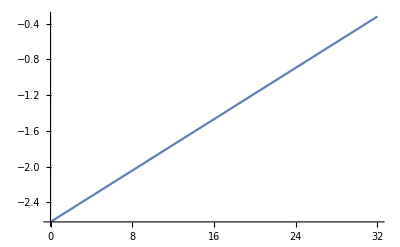

```mathematica
forFit=data⟦2;;,{1,3}⟧;
forFitCr=data⟦2;;,-1⟧;
fit2=LinearModelFit[forFit,{1,x, x^2},x]
fit2@"ParameterTable"
Plot[fit2["Function"]@x, {x, 0, 32}]
```

```mathematica
((print@fit2["FitResiduals"])/(print@forFitCr))^2
χ22=Total[(fit2["FitResiduals"]/forFitCr)^2]/(11-3)
```

{-0.0070866,-0.0270566,0.102243,0.178412,0.457193,-1.48054,-0.740324,2.71997,-1.11976,-0.0555497,-0.0275028}

{0.284416,0.418708,0.547498,0.730806,0.817026,0.888347,0.976613,0.99341,1.18316,1.27402,1.33372}

{0.00062082,0.00417565,0.0348741,0.0596,0.313132,2.77764,0.574643,7.4967,0.895699,0.00190113,0.000425231}

1.51993

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

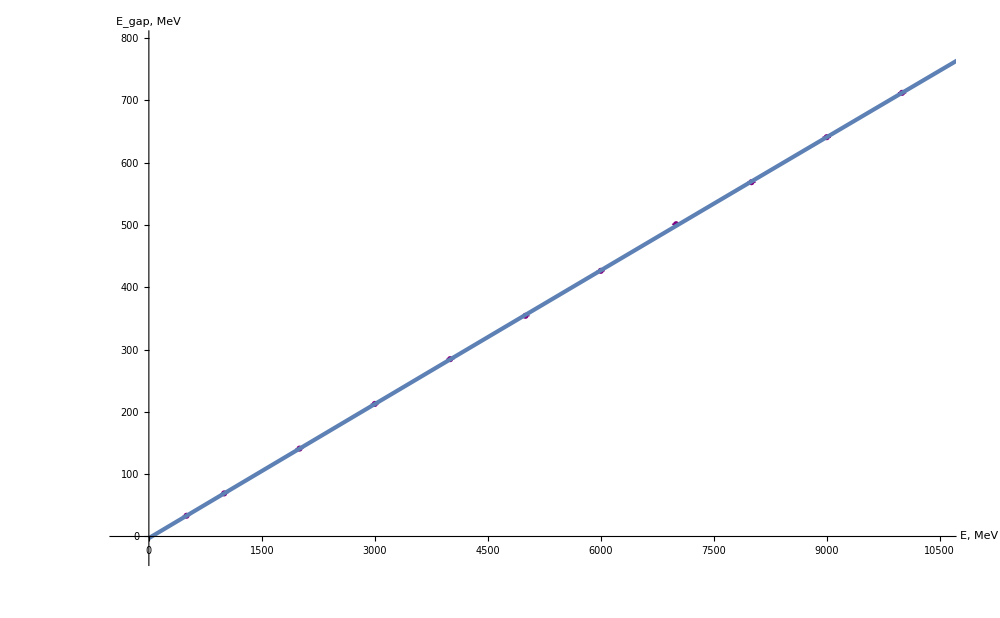

images/png/calib2.png

images/png/fit_res2.png

```mathematica
plot2 =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{-30,795}}], 
Plot[fit2["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["images/png/calib2.png",plot2,"PNG"]
Export["images/png/fit_res2.png",fit2@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportE = {fit2@"BestFitParameters",fit2@"ParameterErrors",χ22}
Export["fit_res2.csv",exportE,"CSV"]
```

{{-2.61836,0.0718575,-3.8481×10^-8},{1.02514,0.000474403,4.47225×10^-8},1.51993}

fit_res2.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
dataR = Import["log_red.csv"];
dataR//TableForm
```

Energy, MeV | Sigma(E), MeV | dE/E | Sigma(dE/E)
874.835 | 6.57889 | 0.193714 | 0.00385103
1354.92 | 8.34461 | 0.15537 | 0.00302056
1936.92 | 9.88635 | 0.127811 | 0.00243474
2966.34 | 12.2489 | 0.104227 | 0.00195122
3555.53 | 12.9824 | 0.100623 | 0.00187349
4132.9 | 14.6888 | 0.0914822 | 0.00170538
4966.54 | 16.5449 | 0.0829272 | 0.00154637
6318.24 | 18.4906 | 0.0726606 | 0.00134465
7129.19 | 20.7577 | 0.0694222 | 0.00128596
7979.78 | 21.1657 | 0.0655433 | 0.00121401
9757.24 | 24.1509 | 0.0593181 | 0.00109316

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.00283894+5.61903/(√x)]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00283894 | 0.00138977 | 2.04274 | 0.0714473
1/(√x) | 5.61903 | 0.0730131 | 76.9592 | 5.34352×10^-14

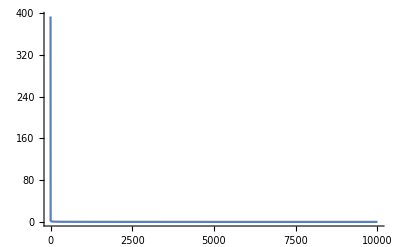

```mathematica
forFitR=dataR⟦2;;,{1,3}⟧;
fitR=LinearModelFit[forFitR,{1,1/Sqrt[x]},x]
forFitCrR=dataR⟦2;;,-1⟧;
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, 0, 10000}, PlotRange->All]
```

```mathematica
((print@fitR["FitResiduals"])/(print@forFitCrR))^2
χR=Total[(fitR["FitResiduals"]/forFitCrR)^2]/(11-2)
```

{0.000899796,-0.000121586,-0.00270251,-0.00178144,0.0035495,0.00123879,0.000355944,-0.000869162,0.000034296,-0.000197833,-0.000405792}

{0.00385103,0.00302056,0.00243474,0.00195122,0.00187349,0.00170538,0.00154637,0.00134465,0.00128596,0.00121401,0.00109316}

{0.0545926,0.00162028,1.23205,0.83355,3.58949,0.527658,0.052983,0.417815,0.000711265,0.0265555,0.137798}

0.76387

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

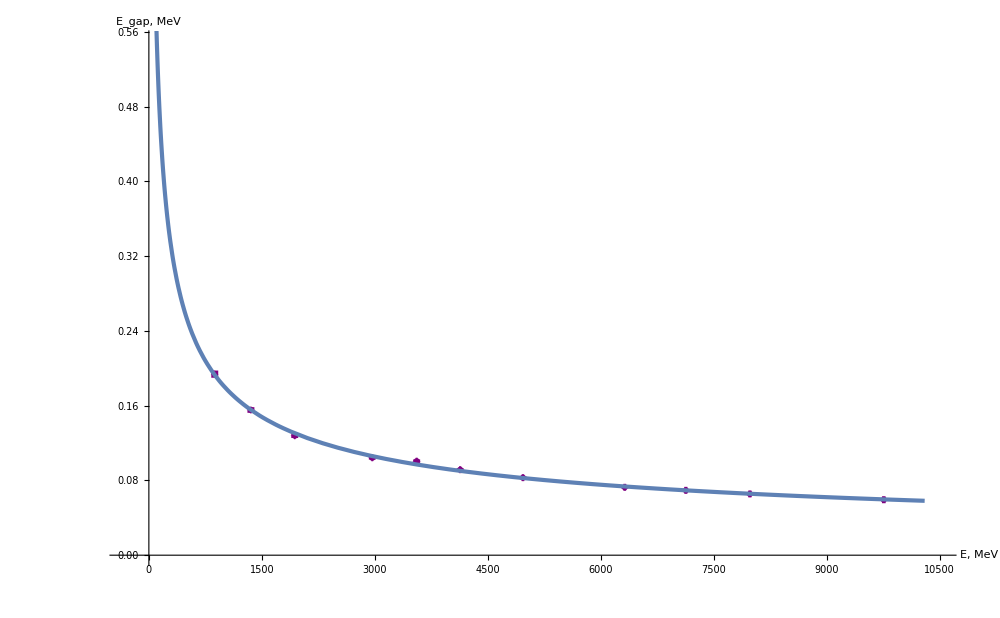

images/png/re.png

images/png/fit_re_res.png

```mathematica
plotR=Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{0,0.55}}], 
Plot[fitR["Function"]@x,{x,0,10300}, PlotStyle->Thickness@0.003, PlotRange->Full]]
Export["images/png/re.png",plotR,"PNG"]
Export["images/png/fit_re_res.png",fitR@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportR = {fitR@"BestFitParameters",fitR@"ParameterErrors",χR}
Export["fit_re_res.csv",exportR,"CSV"]
```

{{0.00283894,5.61903},{0.00138977,0.0730131},0.76387}

fit_re_res.csv